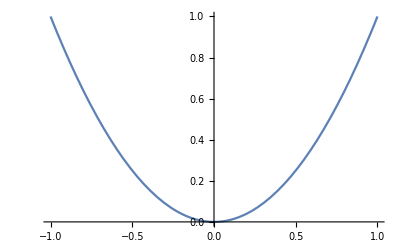

```mathematica
(* Basic 1D plot *)
Plot[x^2, {x,-1,1}]
```

-3+x+x^2

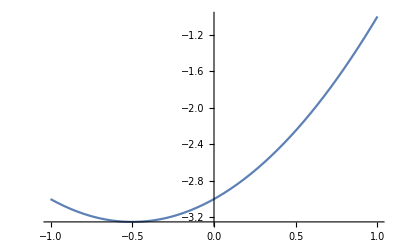

```mathematica
(* Plotting a 1D function *)
fx = x^2 + x -3
Plot[fx, {x,-1,1}]
```



```mathematica
(* Plotting a known function *)
Plot[Sin[x], {x,0,2Pi}]
```

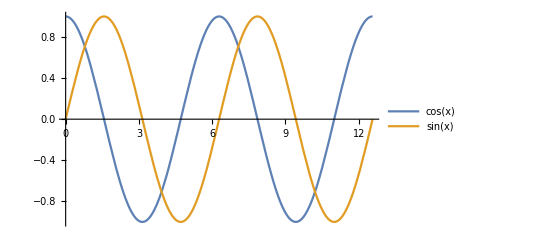

```mathematica
(* Plotting multiple functions with labels *)
(* Notice the curly braces *)
Plot[{Cos[x],Sin[x]}, {x, 0, 4Pi},PlotLegends -> "Expressions"]
```

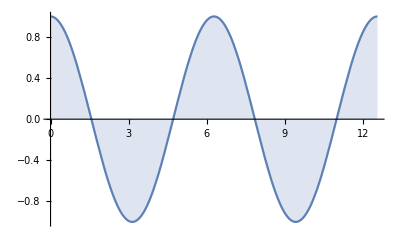

```mathematica
(* Plotting with fill *)
Plot[Cos[x], {x,0,4Pi}, Filling -> Axis]
```

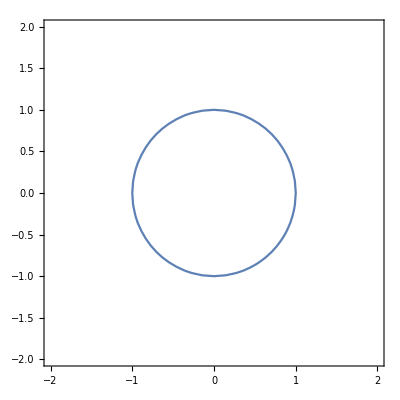

```mathematica
(* Plotting implicit equations *)
ContourPlot[x^2 + y^2 == 1, {x,-2,2}, {y,-2,2}]
```